# Comparison of Single-Winner Voting Systems

Adam Rumpf, 10/31/2017

## Introduction

This demonstration simulates a single-winner election between 2-5 candidates using four common voting systems. The voting population is assumed to follow a normal distribution along a single ideological spectrum, while each candiate’s position lies at a specific point on the spectrum. The bell curve can be colored to display either regions where each candidate is the favorite, or intervals over which voters approve of each candidate. The text underneath the bell curve shows which candidate would win under each method for the given voter distribution, while the colored bars show which candidate would win if the mean voter (a.k.a. the center of opinion, indicated by a gray line underneath the bell curve) were centered at each point on the spectrum.

The purpose of this demonstration is to show how much of an impact the voting system can have on an election. In a single-winner election with only two candidates there is obviously only one fair way to decide on the winner: ask each voter which candidate they prefer and take the candidate that more voters prefer. When there are more than two candidates it is not nearly as straightforward, and different voting systems can produce different results.

Four common voting methods are included in this Notebook: first-past-the-post (FPTP, a.k.a. plurality voting), instant-runoff voting (IRV, a.k.a. alternative vote, transferable vote, or hare), Borda Count, and Approval Voting. The first three are ranked voting systems while approval voting is a cardinal system. Their rules are as follows:

FPTP: This is the system that most people are familiar with. Each voter gets to vote for one candidate, and the candidate with the most votes wins. We assume that each voter votes for the candidate ideologically closest to them

IRV: Each voter gets to rank the candidates from their first choice to their last chocie, with no ties allowed. The votes are then tallied by applying all of the first-choice votes to the appropriate candidates. If one candidate has a strict majority, then they win, and otherwise the candidate in last place is eliminated. All of the votes that originally ranked this candidate first are then moved to their second choice candidates and the process is repeated. Candidates are iteratively dropped and their votes are moved down the preference lists until one candidate achieves a majority. We assume that each voter ranks candidates from ideologically closest to ideologically farthest.

Borda Count: Each voter ranks candidates exactly as in IRV. The votes are then tallied by giving each candidate points based on their rankings on each ballot. If there are n candidates, then every fist-choice vote is worth n points, every second-choice vote is worth n-1 points, every third-choice vote is worth n-2 points, and so on, until finally every last-choice vote is worth 1 point. The candidate with the highest total score wins. We again assume that each voter ranks candidates from ideologically closest to ideologically farthest.

Approval Voting: This is a very minor modification of FPTP. Each voter gets to vote for as many candidates as they wish, and the candidate with the most votes wins. We assume that each voter has a set approval range which defines an interval of the ideological spectrum, and that they will vote for any and all candidates within that range and no candidate outside of this range. If no candidate falls within their approval range, then they abstain.

The Code section of this Notebook includes three sections: initialization code, a collection of particular examples that illustrate particular phemonena, and finally a Manipulate environment that allows the user to play with an interactive model.

## Code

### Initialization

```mathematica
(* Given a list of party positions, returns a list of every preference list that voters would actually write down, each followed by a list of ranges on which voters would choose that list. *)
prefbreaks[p_,ends_:{-3,3}]:=Module[{n=Length[p],break,pair,mid,dist,pref,used={},int={},temp},
(* n = number of parties
break = list of breaks (halfway between each possible pair of parties)
pair = list of unordered pairs of party positions
mid = midpoints between each break point, to use as a sample for order calculation
dist = pairwise distances from each midpoint to each party
pref = preference lists corresponding to each subinterval
used = list of used preference lists
int = list of interval lists *)
pair=Subsets[p,{2}];
break=Sort[Join[Table[Mean[(pair[[i]])],{i,1,Length[pair]}],ends]];
mid=Table[Mean[{break[[i]],break[[i+1]]}],{i,1,Length[break]-1}];
dist=Table[Abs[(mid[[i]])-(p[[j]])],{i,1,Length[mid]},{j,1,n}];
pref=Table[Ordering[dist[[i]]],{i,1,Length[dist]}];
Do[
(* keep a running list of intervals for each used preference list *)
(*temp=Position[used,(pref[[i]])];*)
(*If[Length[temp]==0,*)
(* if new, add to used list *)
used=Append[used,(pref[[i]])];
temp=Length[used];
int=Append[int,{break[[i]],break[[i+1]]}];(*int=Append[int,{{break[[i]],break[[i+1]]}}],*)
(* otherwise, find the position of the existing element *)
(*temp=temp[[1,1]];*)
(*int[[temp]]=Append[int[[temp]],{break[[i]],break[[i+1]]}];*)
(*]*),
{i,1,Length[pref]}];
{used,int}
];
(* Given a list of party positions and an approval tolerance, returns a list of intervals over which voters would approve of the corresponding party.  We assume for now that voters abstain if there are no parties in range. *)
appbreaks[p_,ϵ_,ends_:{-3,3}]:=Table[{Max[ends[[1]],p[[i]]-ϵ],Min[ends[[2]],p[[i]]+ϵ]},{i,1,Length[p]}];
normalint[μ_,σs_,a_,b_]:=N[1/2(Erf[(b-μ)/(√2 σs)]-Erf[(a-μ)/(√2 σs)])];
(* Given a list of intervals and a list of distribution parameters, produces a list of integrals for each parameter. *)
intlist[μ_,σs_,list_]:=Table[normalint[μ,σs,list[[i,1]],list[[i,2]]],{i,1,Length[list]}];
(* Given a preference list, a vote share, and a list of how much each position is worth, calculates the total score given to every party from this particular preference list. *)
listscore[pref_,votes_,score_]:=Module[{out=ConstantArray[0,Length[pref]]},
Do[
out[[(pref[[i]])]]=votes*score[[i]],
{i,1,Length[pref]}];
out
];
(* Given a list of preference lists, a list of their corresponding voter totals, and a list of how much each position is worth, calculates a total score for each party. *)
totscore[pref_,votes_,score_]:=Module[{tot=ConstantArray[0,Length[pref[[1]]]]},
Do[
tot+=listscore[pref[[i]],votes[[i]],score],
{i,1,Length[pref]}];
tot
];
(* Given a list of scores, returns the winning party. *)
winner[list_]:=Ordering[list][[-1]];
(* Score lists for each voting system as a function of the number of parties.
-FTPT: 1 for first, 0 otherwise
-Antiplurality: -1 for last, 0 otherwise
-Borda: position i gets n-i *)
scorefptp[n_]:=Prepend[ConstantArray[0,n-1],1];
scoreantiplur[n_]:=Append[ConstantArray[0,n-1],-1];
scoreborda[n_]:=Table[n-i,{i,1,n}];
(* Given a list of preference lists and corresponding voting shares, conducts an instant runoff vote and returns the winner. *)
irvwinner[prefin_,votes_]:=Module[{pref=prefin,n=Length[prefin[[1]]],m=Length[prefin],goal,tot,out,gone={}},
(* n = number of parties
m = number of preference lists
goal = number of votes needed to achieve a majority (half of total votes)
tot = running total votes for each party
out = winning party
gone = eliminated parties *)
goal=Total[votes]/2;
tot=ConstantArray[0,n];
(* This works similarly to the two-round algorithm, except that instead of maintaining a list of top candidates we maintain a list of eliminated candidates, and the main loop can go around more than once.  We end if any party passes the goal, or if there's only one party left.  We begin "out" at -1, and keep it negative until we find the winner. *)
out=-1;
While[out<0,
Do[(* Add up first choice votes. *)
tot[[(pref[[i,1]])]]+=votes[[i]],
{i,1,m}];
If[Max[tot]≥goal,
(* If we have a majority, that party wins. *)
out=Ordering[tot][[-1]],
(* Otherwise, eliminate the last place party and transfer their vote shares down their preference lists until reaching a valid candidate. *)
gone=Append[gone,Ordering[tot][[Length[gone]+1]]];
tot=ConstantArray[0,n];
Do[(* Process each preference list. *)
While[MemberQ[gone,pref[[i,1]]]==True,(* Move down the list until hitting a party not in the eliminated list. *)
pref[[i]]=Delete[pref[[i]],1];
],
{i,1,m}];
];
];
out
];
(* Given a list of party positions and voter distribution and approval parameters and a voting method, acts as a driver to calculate the winner under each voting system. *)
driver1[p_,μ_,σ_,ϵ_,w_]:=Module[{n=Length[p],pref,breaks,votes,tot,out},
(* pref = preference lists
breaks = preference list or approval intervals
app = approval intervals
votes = vote share within each interval
tot = scores
out = output *)
Switch[w,
1,(* FPTP *)
{pref,breaks}=prefbreaks[p];
votes=intlist[μ,σ^2,breaks];
tot=totscore[pref,votes,scorefptp[n]];
out=winner[tot],
3,(* Borda Count *)
{pref,breaks}=prefbreaks[p];
votes=intlist[μ,σ^2,breaks];
tot=totscore[pref,votes,scoreborda[n]];
out=winner[tot],
4,(* Approval *)
breaks=appbreaks[p,ϵ];
tot=intlist[μ,σ^2,breaks];
out=winner[tot],
6,(* IRV *)
{pref,breaks}=prefbreaks[p];
votes=intlist[μ,σ^2,breaks];
out=irvwinner[pref,votes];
];
out
];
(* Applies driver1 to a given party position list and variance list, overa a variety of population means.  You can also specify the number of nodes on [-3,3]. *)
μsweep[p_,σ_,ϵ_,w_,n_:101]:=Table[driver1[p,μ,σ,ϵ,w],{μ,-3,3,6/(n-1)}];
(* Party colors, in order. *)
colors={Red,Green,RGBColor[1,0.8,0],Blue,Magenta};
(* Same as μsweep, except that it shows a bar of party colors instead of numbers. *)
μsweepcolor[p_,σ_,ϵ_,w_,n_:101,xr_:{-1,1},yr_:{-1,1}]:=ArrayPlot[{μsweep[p,σ,ϵ,w,n]},ColorRules->Table[i->colors[[i]],{i,1,Length[colors]}],DataRange->{xr,yr}];
(* Given the voter mean and standard deviation, and party position list, draws the voter bell curve with regions colored according to closest party. *)
bellcurve[μ_,σ_,pos_]:=Module[{order,breaks},
(* Find the halfway point between each adjacent pair of preferences, and color the intervals accordingly. *)
order=Ordering[pos];
breaks=Join[{-3},Table[N[(pos[[(order[[i+1]])]]+pos[[(order[[i]])]])/2],{i,1,Length[order]-1}],{3}];
Show[Table[Plot[PDF[NormalDistribution[μ,σ^2],x],{x,breaks[[i]],breaks[[i+1]]},Axes->False,AxesOrigin->{0,0},PlotStyle->Opacity[0],Filling->Axis,FillingStyle->colors[[(order[[i]])]]],{i,1,Length[breaks]-1}],PlotRange->All]
];
(* Grey bell curve with transparent approval intervals. *)
bellcurveshade[μ_,σ_,p_,ϵ_]:=Module[{int},
int=appbreaks[p,ϵ];
Show[Join[{Plot[PDF[NormalDistribution[μ,σ^2],x],{x,-3,3},Axes->False,AxesOrigin->{0,0},PlotStyle->LightGray,Filling->Axis,FillingStyle->LightGray]},Table[Plot[PDF[NormalDistribution[μ,σ^2],x],{x,int[[i,1]],int[[i,2]]},Axes->False,AxesOrigin->{0,0},PlotStyle->{colors[[i]],Opacity[0.25]},Filling->Axis,FillingStyle->{colors[[i]],Opacity[0.25]}],{i,1,Length[p]}]]]
];
(* Given a list of party positions, draws vertical lines showing these positions. *)
partylines[pos_]:=Graphics[Flatten[Table[{Black,Thickness[0.008],Line[{{pos[[i]],-0.1},{pos[[i]],0.75}}],colors[[i]],Thickness[0.004],Line[{{pos[[i]],-0.1},{pos[[i]],0.75}}]},{i,1,Length[pos]}]]];
(* Maps party numbers to candidate letters. *)
let[1]:="A";
let[2]:="B";
let[3]:="C";
let[4]:="D";
let[5]:="E";
```

### Particular Examples

#### Spoiler Effect of FPTP

The image below shows a situation in which center-left candidate A is nearest the center of opinion, and is thus agreeable to the most people, but does not win under FPTP. This is because of the presence of the left-leaning candidate C acting as a spoiler. If C were not in the race then A would easily win, but C absorbs enough left-leaning votes that would have otherwise gone to A that the center-right candidate B can easily win, in spite of the fact that A is closer to most peoples’ positions.

This problem does not occur in any of the other systems, which take measures specifically meant to avoid the spoiler effect. IRV, in particular, is designed to allow supporters of third-party candidates to safely rank their true favorite candidate first, while still allowing them to express their preference among the major candidates in case their true favorite doesn’t win. In this case, everyone who ranked C first happens to have also ranked A second, and so after C is eliminated their votes go to A, which is where they would have gone if C had not been in the race to begin with.

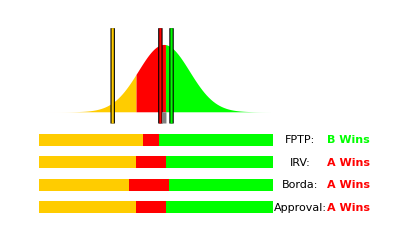

```mathematica
Module[{n=101,p,pref,w={0,0,0,0,0,0},g,μ=0.22,σ=0.815,ϵ=0.6,np=3,p1=0.12,p2=0.41,p3=-1.12,p4=-2,p5=2,shading="favorite party"},
(* List of party positions, limited to the parties being used. *)
p=Switch[np,1,{p1},2,{p1,p2},3,{p1,p2,p3},4,{p1,p2,p3,p4},5,{p1,p2,p3,p4,p5}];
(* Calculate winners under the current distribution. *)
w[[1]]=driver1[p,μ,σ,ϵ,1];
w[[3]]=driver1[p,μ,σ,ϵ,3];
w[[4]]=driver1[p,μ,σ,ϵ,4];
w[[6]]=driver1[p,μ,σ,ϵ,6];
(* Show results. *)
g=If[shading=="favorite party",bellcurve[μ,σ,p],bellcurveshade[μ,σ,p,ϵ]];
Show[g,partylines[p],Graphics[{Gray,Thickness[0.008],Line[{{μ,0},{μ,-0.1}}]}],μsweepcolor[p,σ,ϵ,1,n,{-3,3},{-0.3,-0.2}],Graphics[{Text[StyleForm["FPTP:"],{3.75,-0.25}]}],Graphics[{Text[StyleForm[let[w[[1]]]<>" Wins",{Bold,colors[[(w[[1]])]]}],{5,-0.25}]}],μsweepcolor[p,σ,ϵ,6,n,{-3,3},{-0.5,-0.4}],Graphics[{Text[StyleForm["IRV:"],{3.75,-0.45}]}],Graphics[{Text[StyleForm[let[w[[6]]]<>" Wins",{Bold,colors[[(w[[6]])]]}],{5,-0.45}]}],Graphics[{Text[StyleForm["Borda:"],{3.75,-0.65}]}],Graphics[{Text[StyleForm[let[w[[3]]]<>" Wins",{Bold,colors[[(w[[3]])]]}],{5,-0.65}]}],μsweepcolor[p,σ,ϵ,3,n,{-3,3},{-0.7,-0.6}],Graphics[{Text[StyleForm["Approval:"],{3.75,-0.85}]}],Graphics[{Text[StyleForm[let[w[[4]]]<>" Wins",{Bold,colors[[(w[[4]])]]}],{5,-0.85}]}],μsweepcolor[p,σ,ϵ,4,n,{-3,3},{-0.9,-0.8}],PlotRange->{{-3.1,5.4},{-1,0.8}}]
]
```

#### Spoiler Effect of IRV

In spite of the fact that IRV is generally promoted as a way of overcoming the spoiler effect, it is not completely free of it. In the system below, candidate C has moved closer to the center of opinion. In the above system, C received the fewest first-choice votes and was eliminated first. Now C has become popular enough that it is A whom is now eliminated first. Because A lies between B and C, some of their second-choice votes go to B and some of them go to C, and this is enough to push B past the halfway mark to be counted as the winner, despite again A being closest to the center of opinion.

FPTP and IRV both tend to squeeze out candidates flanked closely by other candidates in a way that Borda and Approval do not. We can also see based on the width of the red bar that Borda tends to be more generous to centrist candidates than Approval.

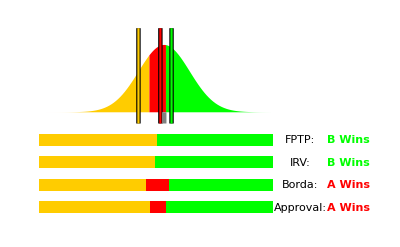

```mathematica
Module[{n=101,p,pref,w={0,0,0,0,0,0},g,μ=0.22,σ=0.815,ϵ=0.6,np=3,p1=0.12,p2=0.41,p3=-0.45,p4=-2,p5=2,shading="favorite party"},
(* List of party positions, limited to the parties being used. *)
p=Switch[np,1,{p1},2,{p1,p2},3,{p1,p2,p3},4,{p1,p2,p3,p4},5,{p1,p2,p3,p4,p5}];
(* Calculate winners under the current distribution. *)
w[[1]]=driver1[p,μ,σ,ϵ,1];
w[[3]]=driver1[p,μ,σ,ϵ,3];
w[[4]]=driver1[p,μ,σ,ϵ,4];
w[[6]]=driver1[p,μ,σ,ϵ,6];
(* Show results. *)
g=If[shading=="favorite party",bellcurve[μ,σ,p],bellcurveshade[μ,σ,p,ϵ]];
Show[g,partylines[p],Graphics[{Gray,Thickness[0.008],Line[{{μ,0},{μ,-0.1}}]}],μsweepcolor[p,σ,ϵ,1,n,{-3,3},{-0.3,-0.2}],Graphics[{Text[StyleForm["FPTP:"],{3.75,-0.25}]}],Graphics[{Text[StyleForm[let[w[[1]]]<>" Wins",{Bold,colors[[(w[[1]])]]}],{5,-0.25}]}],μsweepcolor[p,σ,ϵ,6,n,{-3,3},{-0.5,-0.4}],Graphics[{Text[StyleForm["IRV:"],{3.75,-0.45}]}],Graphics[{Text[StyleForm[let[w[[6]]]<>" Wins",{Bold,colors[[(w[[6]])]]}],{5,-0.45}]}],Graphics[{Text[StyleForm["Borda:"],{3.75,-0.65}]}],Graphics[{Text[StyleForm[let[w[[3]]]<>" Wins",{Bold,colors[[(w[[3]])]]}],{5,-0.65}]}],μsweepcolor[p,σ,ϵ,3,n,{-3,3},{-0.7,-0.6}],Graphics[{Text[StyleForm["Approval:"],{3.75,-0.85}]}],Graphics[{Text[StyleForm[let[w[[4]]]<>" Wins",{Bold,colors[[(w[[4]])]]}],{5,-0.85}]}],μsweepcolor[p,σ,ϵ,4,n,{-3,3},{-0.9,-0.8}],PlotRange->{{-3.1,5.4},{-1,0.8}}]
]
```

#### Non-Monotonicity of IRV

IRV can also display some unusual properties that the other voting systems do not, such as non-monotonicity. Normally one would expect that a candidate should do better if the center of opinion moves closer to them and worse if the center of opinion moves farther from them: this property is called monotonicity. In IRV, that is not always the case.

In the system below, in IRV, candidate A is currently the winner, and is currently to the right of the center of opinion. If the center of opinion moves to the right, and therefore closer to A, we should expect A to do better, but instead we enter a region where B becomes the winner instead of A. This property is indicated by discontinuous bands of color in the IRV bar.

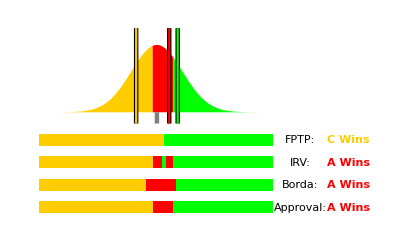

```mathematica
Module[{n=101,p,pref,w={0,0,0,0,0,0},g,μ=0.03,σ=0.815,ϵ=0.6,np=3,p1=0.35,p2=0.57,p3=-0.51,p4=-2,p5=2,shading="favorite party"},
(* List of party positions, limited to the parties being used. *)
p=Switch[np,1,{p1},2,{p1,p2},3,{p1,p2,p3},4,{p1,p2,p3,p4},5,{p1,p2,p3,p4,p5}];
(* Calculate winners under the current distribution. *)
w[[1]]=driver1[p,μ,σ,ϵ,1];
w[[3]]=driver1[p,μ,σ,ϵ,3];
w[[4]]=driver1[p,μ,σ,ϵ,4];
w[[6]]=driver1[p,μ,σ,ϵ,6];
(* Show results. *)
g=If[shading=="favorite party",bellcurve[μ,σ,p],bellcurveshade[μ,σ,p,ϵ]];
Show[g,partylines[p],Graphics[{Gray,Thickness[0.008],Line[{{μ,0},{μ,-0.1}}]}],μsweepcolor[p,σ,ϵ,1,n,{-3,3},{-0.3,-0.2}],Graphics[{Text[StyleForm["FPTP:"],{3.75,-0.25}]}],Graphics[{Text[StyleForm[let[w[[1]]]<>" Wins",{Bold,colors[[(w[[1]])]]}],{5,-0.25}]}],μsweepcolor[p,σ,ϵ,6,n,{-3,3},{-0.5,-0.4}],Graphics[{Text[StyleForm["IRV:"],{3.75,-0.45}]}],Graphics[{Text[StyleForm[let[w[[6]]]<>" Wins",{Bold,colors[[(w[[6]])]]}],{5,-0.45}]}],Graphics[{Text[StyleForm["Borda:"],{3.75,-0.65}]}],Graphics[{Text[StyleForm[let[w[[3]]]<>" Wins",{Bold,colors[[(w[[3]])]]}],{5,-0.65}]}],μsweepcolor[p,σ,ϵ,3,n,{-3,3},{-0.7,-0.6}],Graphics[{Text[StyleForm["Approval:"],{3.75,-0.85}]}],Graphics[{Text[StyleForm[let[w[[4]]]<>" Wins",{Bold,colors[[(w[[4]])]]}],{5,-0.85}]}],μsweepcolor[p,σ,ϵ,4,n,{-3,3},{-0.9,-0.8}],PlotRange->{{-3.1,5.4},{-1,0.8}}]
]
```

### Interactive Module

```mathematica
Manipulate[Module[{n=101,p,pref,w={0,0,0,0,0,0},g},
(* List of party positions, limited to the parties being used. *)
p=Switch[np,1,{p1},2,{p1,p2},3,{p1,p2,p3},4,{p1,p2,p3,p4},5,{p1,p2,p3,p4,p5}];
(* Calculate winners under the current distribution. *)
w[[1]]=driver1[p,μ,σ,ϵ,1];
w[[3]]=driver1[p,μ,σ,ϵ,3];
w[[4]]=driver1[p,μ,σ,ϵ,4];
w[[6]]=driver1[p,μ,σ,ϵ,6];
(* Show results. *)
g=If[shading=="favorite party",bellcurve[μ,σ,p],bellcurveshade[μ,σ,p,ϵ]];
Show[g,partylines[p],Graphics[{Gray,Thickness[0.008],Line[{{μ,0},{μ,-0.1}}]}],μsweepcolor[p,σ,ϵ,1,n,{-3,3},{-0.3,-0.2}],Graphics[{Text[StyleForm["FPTP:"],{3.75,-0.25}]}],Graphics[{Text[StyleForm[let[w[[1]]]<>" Wins",{Bold,colors[[(w[[1]])]]}],{5,-0.25}]}],μsweepcolor[p,σ,ϵ,6,n,{-3,3},{-0.5,-0.4}],Graphics[{Text[StyleForm["IRV:"],{3.75,-0.45}]}],Graphics[{Text[StyleForm[let[w[[6]]]<>" Wins",{Bold,colors[[(w[[6]])]]}],{5,-0.45}]}],Graphics[{Text[StyleForm["Borda:"],{3.75,-0.65}]}],Graphics[{Text[StyleForm[let[w[[3]]]<>" Wins",{Bold,colors[[(w[[3]])]]}],{5,-0.65}]}],μsweepcolor[p,σ,ϵ,3,n,{-3,3},{-0.7,-0.6}],Graphics[{Text[StyleForm["Approval:"],{3.75,-0.85}]}],Graphics[{Text[StyleForm[let[w[[4]]]<>" Wins",{Bold,colors[[(w[[4]])]]}],{5,-0.85}]}],μsweepcolor[p,σ,ϵ,4,n,{-3,3},{-0.9,-0.8}],PlotRange->{{-3.1,5.4},{-1,0.8}}]
],
Style["voter distribution",14,Bold],{{μ,0,"mean"},-3,3},{{σ,1,"std dev"},0.75,1.5},{{ϵ,0.6,"approval range"},0.1,3},Delimiter,Style["candidate positions",14,Bold],{{np,3,"candidates"},2,5,1,RadioButton},{{p1,0,Style["A",{Bold,colors[[1]]}]},-3,3},{{p2,1,Style["B",{Bold,colors[[2]]}]},-3,3},{{p3,-1,Style["C",{Bold,colors[[3]]}]},-3,3},{{p4,-2,Style["D",{Bold,colors[[4]]}]},-3,3},{{p5,2,Style["E",{Bold,colors[[5]]}]},-3,3},Delimiter,Style["display",14,Bold],{{shading,"favorite party","shading"},{"favorite party","approval range"},RadioButton},SaveDefinitions->True]
```